{{o→InterpolatingFunction[…],y→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

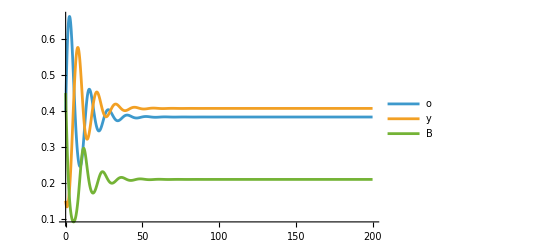

```mathematica
fitO=o[t]+0.5*y[t]+3*B[t];
fitY=2*o[t]+y[t]+0.2*B[t];
fitB=o[t]*0.5+2*y[t]+B[t];

fitmedio=fitO*o[t]+fitY*y[t]+fitB*B[t];

dodt=o[t]*(fitO-fitmedio);
dydt=y[t]*(fitY-fitmedio);
dbdt=B[t]*(fitB-fitmedio);

sol = NDSolve[{o'[t]==dodt,y'[t]==dydt,B'[t]==dbdt,o[0]==0.4,y[0]==0.15,B[0]==0.45},{o,y,B},{t,0,200}]
Plot[{o[t]/. sol[[1]],y[t]/. sol[[1]],B[t]/. sol[[1]]},{t,0,200},PlotLegends->{"o","y","B"}]
```

{{o→InterpolatingFunction[…],y→InterpolatingFunction[…],B→InterpolatingFunction[…]}}

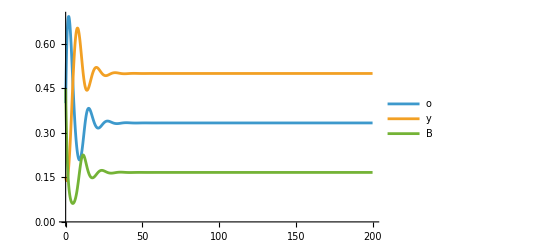

```mathematica
fitO=o[t]+0.5*y[t]+4.5*B[t];
fitY=2*o[t]+y[t]+0.9999*B[t];
fitB=o[t]*0.5+2*y[t]+B[t];

fitmedio=fitO*o[t]+fitY*y[t]+fitB*B[t];

dodt=o[t]*(fitO-fitmedio);
dydt=y[t]*(fitY-fitmedio);
dbdt=B[t]*(fitB-fitmedio);

sol = NDSolve[{o'[t]==dodt,y'[t]==dydt,B'[t]==dbdt,o[0]==0.4,y[0]==0.15,B[0]==0.45},{o,y,B},{t,0,200}]
Plot[{o[t]/. sol[[1]],y[t]/. sol[[1]],B[t]/. sol[[1]]},{t,0,200},PlotLegends->{"o","y","B"}]
```